```mathematica
{"Ωc^* 3/2+ 2.766"}
SuperStar[Ωc]=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,-8/3,0},{0,0,0,0}},2Bcs]
SuperStar[rΩc]=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},SuperStar[Ωc]];
SuperStar[μΩc]=MagneticMoment[{0,1,2,0,0},{0,0,0,0,0},SuperStar[Ωc]];
{SuperStar[rΩc]}
{{SuperStar[μΩc]},{SuperStar[μΩc]/μNp}}
```

{Λc 1/2+ 2.287}

{2.26862,4.86239,{3.07845,2.95307,2.47978,2.04279}}

{0.603089}

{{0.187129},{0.177247}}

{Σc 1/2+ 2.454}

{2.41032,4.81814,{3.07788,2.95147,2.47715,2.04279}}

{0.915348,0.597818,0.350842}

{{0.804096,0.154303,-0.49549},{0.761633,0.146155,-0.469323}}

{Σc^* 3/2+ 2.518}

{2.51073,5.00786,{3.08027,2.95813,2.4883,2.04279}}

{0.950777,0.620418,0.366253}

{{1.53866,0.525591,-0.487478},{1.4574,0.497835,-0.461735}}

{D 0- 1.867}

{1.83421,3.62982,{3.05734,2.89636,2.39956,2.04279}}

{0.456083,0.254338,0.254338,0.456083}

{D^* 1- 2.009}

{2.00782,4.08951,{3.06667,2.92094,2.43125,2.04279}}

{0.510962,0.291651,0.291651,0.510962}

{{0.457674,-0.369616,0.369616,-0.457674},{0.433504,-0.350097,0.350097,-0.433504}}

{Λb 1/2+ 5.620}

{5.64525,4.59735,{3.07485,2.94312,2.46377,2.04279}}

{0.254016}

{{-0.0323766},{-0.0306668}}

{Σb 1/2+ 5.813}

{5.83156,4.63689,{3.07541,2.94466,2.4662,2.04279}}

{0.714619,0.256269,0.6159}

{{0.844592,0.219244,-0.406105},{0.79999,0.207666,-0.384659}}

{Σb^* 3/2+ 5.833}

{5.86928,4.72784,{3.07667,2.94814,2.47173,2.04279}}

{0.728692,0.261452,0.627915}

{{1.24283,0.286411,-0.67001},{1.1772,0.271286,-0.634628}}

{B 0- 5.280}

{5.24533,3.14151,{3.04453,2.8639,2.36329,2.04279}}

{0.418375,0.170957,0.418375}

{B^* 1- 5.325}

{5.32227,3.47526,{3.05367,2.88689,2.38838,2.04279}}

{0.462454,0.190017,0.190017,0.462454}

{{0.500806,-0.202225,0.202225,-0.583811},{0.474359,-0.191546,0.191546,-0.552981}}

{My Error}

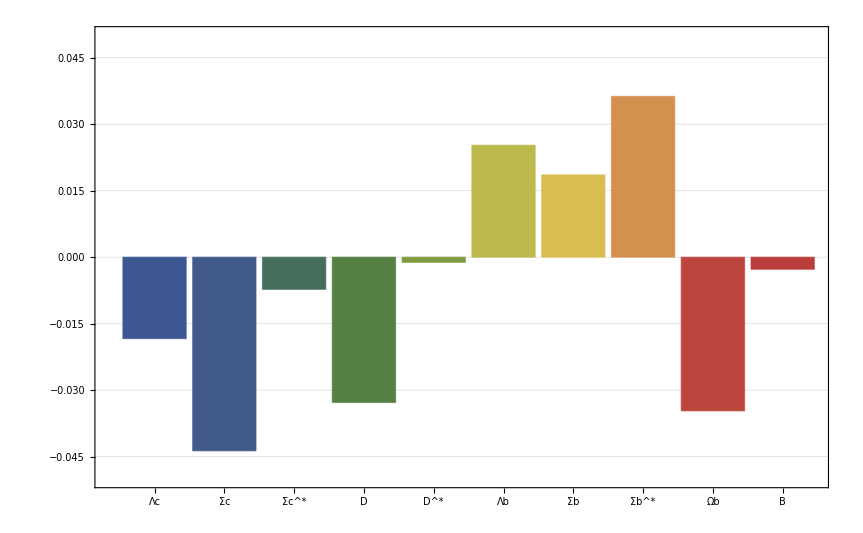

{Charge Radius}

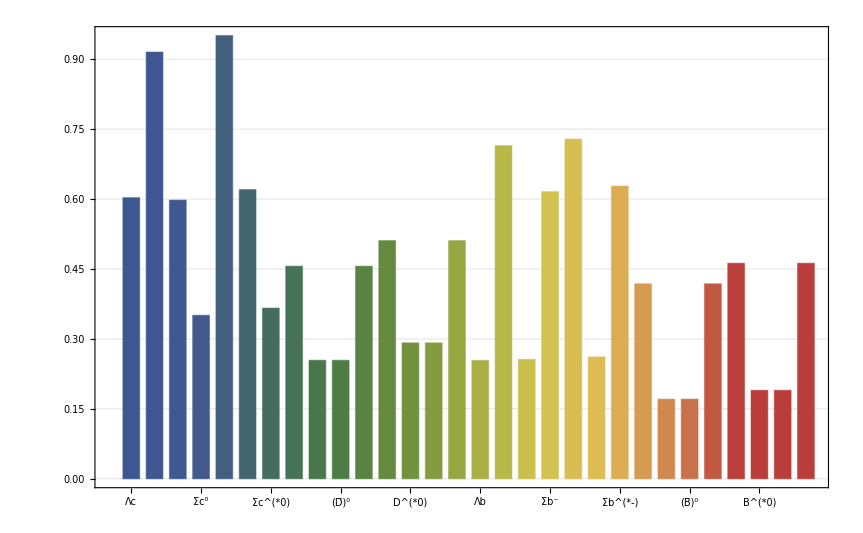

{Magnetic Moment}

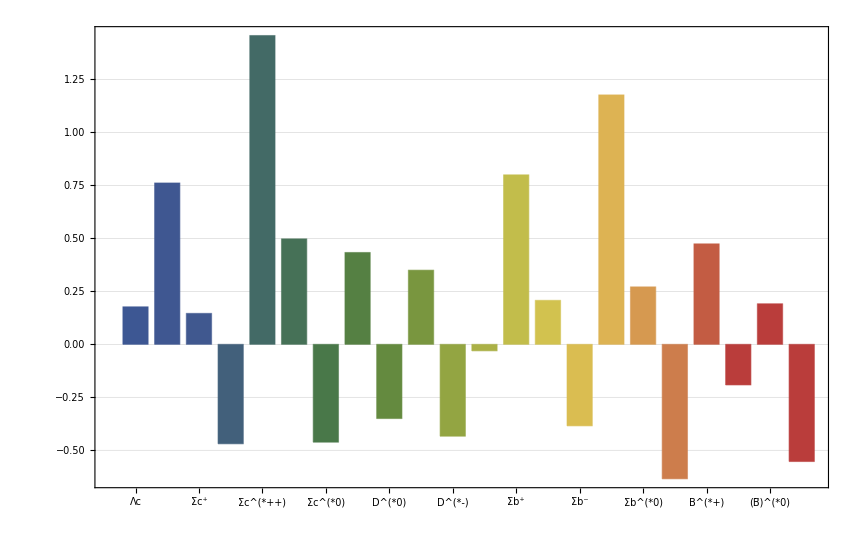

```mathematica
<<MITBagModel\MITBagModel.m

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];

{"Λc 1/2+ 2.287"}
Λc=Hadron[{0,1,0,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0]
rΛc=ChargeRadius[{0,1,0,1,1},{0,0,0,0,0},Λc];
μΛc=MagneticMoment[{0,1,0,0,0},{0,0,0,0,0},Λc];
{rΛc}
{{μΛc},{μΛc/μNp}}

{"Σc 1/2+ 2.454"}
Σc=Hadron[{0,1,0,2},{{0,0,0,0},{0,0,0,32/3},{0,0,0,0},{0,0,0,-8/3}},0]
rΣcpp=ChargeRadius[{0,1,0,2,0},{0,0,0,0,0},Σc];
rΣcp=ChargeRadius[{0,1,0,1,1},{0,0,0,0,0},Σc];
rΣc0=ChargeRadius[{0,1,0,0,2},{0,0,0,0,0},Σc];
μΣcpp=MagneticMoment[{0,-1/3,0,4/3,0},{0,0,0,0,0},Σc];μΣcp=MagneticMoment[{0,-1/3,0,2/3,2/3},{0,0,0,0,0},Σc];μΣc0=MagneticMoment[{0,-1/3,0,0,4/3},{0,0,0,0,0},Σc];
{rΣcpp,rΣcp,rΣc0}
{{μΣcpp,μΣcp,μΣc0},{μΣcpp/μNp,μΣcp/μNp,μΣc0/μNp}}

{"Σc^* 3/2+ 2.518"}
SuperStar[Σc]=Hadron[{0,1,0,2},{{0,0,0,0},{0,0,0,-16/3},{0,0,0,0},{0,0,0,-8/3}},0]
SuperStar[rΣcpp]=ChargeRadius[{0,1,0,2,0},{0,0,0,0,0},SuperStar[Σc]];
SuperStar[rΣcp]=ChargeRadius[{0,1,0,1,1},{0,0,0,0,0},SuperStar[Σc]];
SuperStar[rΣc0]=ChargeRadius[{0,1,0,0,2},{0,0,0,0,0},SuperStar[Σc]];
SuperStar[μΣcpp]=MagneticMoment[{0,1,0,2,0},{0,0,0,0,0},SuperStar[Σc]];
SuperStar[μΣcp]=MagneticMoment[{0,1,0,1,1},{0,0,0,0,0},SuperStar[Σc]];
SuperStar[μΣc0]=MagneticMoment[{0,1,0,0,2},{0,0,0,0,0},SuperStar[Σc]];
{SuperStar[rΣcpp],SuperStar[rΣcp],SuperStar[rΣc0]}
{{SuperStar[μΣcpp],SuperStar[μΣcp],SuperStar[μΣc0]},{SuperStar[μΣcpp]/μNp,SuperStar[μΣcp]/μNp,SuperStar[μΣc0]/μNp}}

{"D 0- 1.867"}
Dq=Hadron[{0,1,0,1},{{0,0,0,0},{0,0,0,16},{0,0,0,0},{0,0,0,0}},0]
rDp=ChargeRadius[{0,1,0,0,0},{0,0,0,0,1},Dq];
rD0=ChargeRadius[{0,1,0,0,0},{0,0,0,1,0},Dq];
rD0bar=ChargeRadius[{0,0,0,1,0},{0,1,0,0,0},Dq];
rDm=ChargeRadius[{0,0,0,0,1},{0,1,0,0,0},Dq];
{rDp,rD0,rD0bar,rDm}

{"D^* 1- 2.009"}
SuperStar[Dq]=Hadron[{0,1,0,1},{{0,0,0,0},{0,0,0,-16/3},{0,0,0,0},{0,0,0,0}},0]
SuperStar[rDp]=ChargeRadius[{0,1,0,0,0},{0,0,0,0,1},SuperStar[Dq]];
SuperStar[rD0]=ChargeRadius[{0,1,0,0,0},{0,0,0,1,0},SuperStar[Dq]];
SuperStar[rD0bar]=ChargeRadius[{0,0,0,1,0},{0,1,0,0,0},SuperStar[Dq]];
SuperStar[rDm]=ChargeRadius[{0,0,0,0,1},{0,1,0,0,0},SuperStar[Dq]];
SuperStar[μDp]=MagneticMoment[{0,1,0,0,0},{0,0,0,0,1},SuperStar[Dq]];
SuperStar[μD0]=MagneticMoment[{0,1,0,0,0},{0,0,0,1,0},SuperStar[Dq]];
SuperStar[μD0bar]=MagneticMoment[{0,0,0,1,0},{0,1,0,0,0},SuperStar[Dq]];
SuperStar[μDm]=MagneticMoment[{0,0,0,0,1},{0,1,0,0,0},SuperStar[Dq]];
{SuperStar[rDp],SuperStar[rD0],SuperStar[rD0bar],SuperStar[rDm]}
{{SuperStar[μDp],SuperStar[μD0],SuperStar[μD0bar],SuperStar[μDm]},{SuperStar[μDp]/μNp,SuperStar[μD0]/μNp,SuperStar[μD0bar]/μNp,SuperStar[μDm]/μNp}}

{"Λb 1/2+ 5.620"}
Λb=Hadron[{1,0,0,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0]
rΛb=ChargeRadius[{1,0,0,1,1},{0,0,0,0,0},Λb];
μΛb=MagneticMoment[{1,0,0,0,0},{0,0,0,0,0},Λb];
{rΛb}
{{μΛb},{μΛb/μNp}}

{"Σb 1/2+ 5.813"}
Σb=Hadron[{1,0,0,2},{{0,0,0,32/3},{0,0,0,0},{0,0,0,0},{0,0,0,-8/3}},0]
rΣbp=ChargeRadius[{1,0,0,2,0},{0,0,0,0,0},Σb];
rΣb0=ChargeRadius[{1,0,0,1,1},{0,0,0,0,0},Σb];
rΣbm=ChargeRadius[{1,0,0,0,2},{0,0,0,0,0},Σb];
μΣbp=MagneticMoment[{-1/3,0,0,4/3,0},{0,0,0,0,0},Σb];μΣb0=MagneticMoment[{-1/3,0,0,2/3,2/3},{0,0,0,0,0},Σb];μΣbm=MagneticMoment[{-1/3,0,0,0,4/3},{0,0,0,0,0},Σb];
{rΣbp,rΣb0,rΣbm}
{{μΣbp,μΣb0,μΣbm},{μΣbp/μNp,μΣb0/μNp,μΣbm/μNp}}

{"Σb^* 3/2+ 5.833"}
SuperStar[Σb]=Hadron[{1,0,0,2},{{0,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,-8/3}},0]
SuperStar[rΣbp]=ChargeRadius[{1,0,0,2,0},{0,0,0,0,0},SuperStar[Σb]];
SuperStar[rΣb0]=ChargeRadius[{1,0,0,1,1},{0,0,0,0,0},SuperStar[Σb]];
SuperStar[rΣbm]=ChargeRadius[{1,0,0,0,2},{0,0,0,0,0},SuperStar[Σb]];
SuperStar[μΣbp]=MagneticMoment[{1,0,0,2,0},{0,0,0,0,0},SuperStar[Σb]];
SuperStar[μΣb0]=MagneticMoment[{1,0,0,1,1},{0,0,0,0,0},SuperStar[Σb]];
SuperStar[μΣbm]=MagneticMoment[{1,0,0,0,2},{0,0,0,0,0},SuperStar[Σb]];
{SuperStar[rΣbp],SuperStar[rΣb0],SuperStar[rΣbm]}
{{SuperStar[μΣbp],SuperStar[μΣb0],SuperStar[μΣbm]},{SuperStar[μΣbp]/μNp,SuperStar[μΣb0]/μNp,SuperStar[μΣbm]/μNp}}

{"B 0- 5.280"}
Bq=Hadron[{1,0,0,1},{{0,0,0,16},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]
rBp=ChargeRadius[{0,0,0,1,0},{1,0,0,0,0},Bq];
rB0=ChargeRadius[{0,0,0,0,1},{1,0,0,0,0},Bq];
rB0bar=ChargeRadius[{1,0,0,0,0},{0,0,0,0,1},Bq];
rBm=ChargeRadius[{1,0,0,0,0},{0,0,0,1,0},Bq];
{rBp,rB0,rBm}

{"B^* 1- 5.325"}
SuperStar[Bq]=Hadron[{1,0,0,1},{{0,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]
SuperStar[rBp]=ChargeRadius[{0,0,0,1,0},{1,0,0,0,0},SuperStar[Bq]];
SuperStar[rB0]=ChargeRadius[{0,0,0,0,1},{1,0,0,0,0},SuperStar[Bq]];
SuperStar[rB0bar]=ChargeRadius[{1,0,0,0,0},{0,0,0,0,1},SuperStar[Bq]];
SuperStar[rBm]=ChargeRadius[{1,0,0,0,0},{0,0,0,1,0},SuperStar[Bq]];
SuperStar[μBp]=MagneticMoment[{0,0,0,1,0},{1,0,0,0,0},SuperStar[Bq]];
SuperStar[μB0]=MagneticMoment[{0,0,0,0,1},{1,0,0,0,0},SuperStar[Bq]];
SuperStar[μB0bar]=MagneticMoment[{1,0,0,0,0},{0,0,0,0,1},SuperStar[Bq]];
SuperStar[μBm]=MagneticMoment[{1,0,0,0,0},{0,0,0,1,0},SuperStar[Dq]];
{SuperStar[rBp],SuperStar[rB0],SuperStar[rB0bar],SuperStar[rBm]}
{{SuperStar[μBp],SuperStar[μB0],SuperStar[μB0bar],SuperStar[μBm]},{SuperStar[μBp]/μNp,SuperStar[μB0]/μNp,SuperStar[μB0bar]/μNp,SuperStar[μBm]/μNp}}

{"My Error"}
BarChart[{
(First[Λc]-2.287),
(First[Σc]-2.454),
(First[SuperStar[Σc]]-2.518),
(First[Dq]-1.867),
(First[SuperStar[Dq]]-2.009),
(First[Λb]-5.620),
(First[Σb]-5.813),
(First[SuperStar[Σb]]-5.833),
(First[Bq]-5.280),
(First[SuperStar[Bq]]-5.325)},Frame->True,ChartLabels->{"Λc","Σc","Σc^*","D","D^*","Λb","Σb","Σb^*","Ωb","B","B^*"},ChartStyle->"DarkRainbow",PlotRange->{-0.05,0.05},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΛc,rΣcpp,rΣcp,rΣc0,SuperStar[rΣcpp],SuperStar[rΣcp],SuperStar[rΣc0],rDp,rD0,rD0bar,rDm,SuperStar[rDp],SuperStar[rD0],SuperStar[rD0bar],SuperStar[rDm],rΛb,rΣbp,rΣb0,rΣbm,SuperStar[rΣbp],SuperStar[rΣb0],SuperStar[rΣbm],rBp,rB0,rB0bar,rBm,SuperStar[rBp],SuperStar[rB0],SuperStar[rB0bar],SuperStar[rBm]},Frame->True,ChartLabels->{"Λc","Σc^(++)","Σc^+","Σc^0","Σc^(*++)","Σc^(*+)","Σc^(*0)","D^+","D^0","(D̄)^0","D^-","D^(*+)","D^(*0)","(D̄)^(*0)","D^(*-)","Λb","Σb^+","Σb^0","Σb^-","Σb^(*+)","Σb^(*0)","Σb^(*-)","B^+","B^0","(B̄)^0","B^-","B^(*+)","B^(*0)","(B̄)^(*0)","B^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΛc/μNp,μΣcpp/μNp,μΣcp/μNp,μΣc0/μNp,SuperStar[μΣcpp]/μNp,SuperStar[μΣcp]/μNp,SuperStar[μΣc0]/μNp,SuperStar[μDp]/μNp,SuperStar[μD0]/μNp,SuperStar[μD0bar]/μNp,SuperStar[μDm]/μNp,μΛb/μNp,μΣbp/μNp,μΣb0/μNp,μΣbm/μNp,SuperStar[μΣbp]/μNp,SuperStar[μΣb0]/μNp,SuperStar[μΣbm]/μNp,SuperStar[μBp]/μNp,SuperStar[μB0]/μNp,SuperStar[μB0bar]/μNp,SuperStar[μBm]/μNp},Frame->True,ChartLabels->{"Λc","Σc^(++)","Σc^+","Σc^0","Σc^(*++)","Σc^(*+)","Σc^(*0)","D^(*+)","D^(*0)","(D̄)^(*0)","D^(*-)","Λb","Σb^+","Σb^0","Σb^-","Σb^(*+)","Σb^(*0)","Σb^(*-)","B^(*+)","B^(*0)","(B̄)^(*0)","B^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```